```mathematica
Needs["ErrorBarPlots`"];
homepath = SetDirectory["H:\\UofT Ultracold Atoms Lab\\Projects\\Conductivity\\data analysis\\2.5Er 3Aug 2017\\20G kick 0\\temp\\U_TempFitting_2.5Er_0Er_pulse_20G_XDT1_0.15_ramp_150ms_60Hz_amp_1pp_xlat_10k_0.1msPin"]
folderlist1 = FileNames["*.mat",homepath];
foldernumber = Length[folderlist1]
```

H:\UofT Ultracold Atoms Lab\Projects\Conductivity\data analysis\2.5Er 3Aug 2017\20G kick 0\temp\U_TempFitting_2.5Er_0Er_pulse_20G_XDT1_0.15_ramp_150ms_60Hz_amp_1pp_xlat_10k_0.1msPin

9

```mathematica
Clear[img,num];
num=0;
pic=ToExpression[Import[folderlist1⟦1⟧]⟦1,1,1⟧];
img=pic-pic;

modfreqss=20;
modtimess=100;
kicktemplatdepthss=6;

For[ii=1,ii≤foldernumber,ii++,
{
s2=StringSplit[folderlist1⟦ii⟧,"\\"]⟦-1⟧;
(*kicktemplatdepth=ToExpression[StringCases[s2,("kick_latdepth="~~code:NumberString)..:>code]⟦1⟧];*)
(*zld=ToExpression[StringCases[s2,("latdepth="~~code:NumberString)..:>code]⟦1⟧];*)
pic=ToExpression[Import[folderlist1⟦ii⟧]⟦1,1,1⟧];

If[  Max[pic]<4000 && Max[pic]>400,{
num=num+1;
img=img+pic;
Print[{Min[pic],Max[pic]}];
}];
}] 
img=img/num;

num

(*to 1D array*)
datalist=Table[{Ceiling[ix/512.], Mod[ix-1,512]+1, img[[Ceiling[ix/512.],Mod[ix-1,512]+1 ]]},{ix,1,512*512}];
```

{-4.,1953.}

{-5.,2016.}

{-5.,1833.}

{-5.,1944.}

{-5.,1796.}

{-4.,1981.}

{-4.,1931.}

{-5.,1701.}

{-5.,1959.}

9

H:\UofT Ultracold Atoms Lab\Projects\Conductivity\data analysis\2.5Er 3Aug 2017\20G kick 0\temp\U_TempFitting_2.5Er_0Er_pulse_20G_XDT1_0.15_ramp_150ms_60Hz_amp_1pp_xlat_10k_0.1msPin\temp.txt

{offset→4.81681,amp1→742.479,x01→262.915,y01→280.854,sigx1→76.6742,sigy1→78.8369}

262.915

280.854

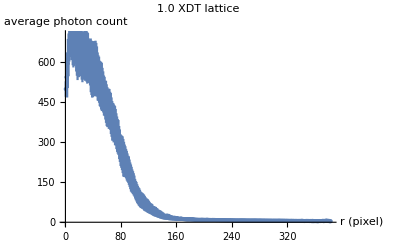

H:\UofT Ultracold Atoms Lab\Projects\Conductivity\data analysis\2.5Er 3Aug 2017\20G kick 0\temp\U_TempFitting_2.5Er_0Er_pulse_20G_XDT1_0.15_ramp_150ms_60Hz_amp_1pp_xlat_10k_0.1msPin\temp.txt

```mathematica
filename=StringJoin[homepath,"\\temp.txt"]

sol=FindFit[datalist,amp1*Exp[-(x-x01)^2/sigx1^2-(y-y01)^2/sigy1^2]+offset,{{offset,0},{amp1,3000},{x01,255},{y01,255},{sigx1,30},{sigy1,30}},{x,y}]
xc=sol⟦3,2⟧
yc=sol⟦4,2⟧
avg=Table[{√((datalist⟦ii,1⟧-xc)^2+(datalist⟦ii,2⟧-yc)^2),datalist⟦ii,3⟧},{ii,1,Length[datalist]}];
avg=Sort[avg,#1⟦1⟧<#2⟦1⟧&];
δx=1;
leng=Length[avg];
startx=0;
endx=startx+δx;
startid=1;
endid=startid;
sumlist={0};
For[ix=1,ix≤leng,ix++,
{
If[
avg⟦ix,1⟧>endx,
{
endid=ix-1;
sumlist=Join[sumlist,{{(startx+endx)/2,Mean[avg⟦startid;;endid,2⟧],√(StandardDeviation[avg⟦startid;;endid,2⟧]^2+Mean[avg⟦startid;;endid,2⟧])}}];
(*Print[{ix,startx,endx,startid,endid}];*)
startid=ix;
startx=endx;
endx=startx+δx;
}
];
}
]
sumlist=sumlist⟦2;;Length[sumlist]⟧;
Needs["ErrorBarPlots`"];
ErrorListPlot[sumlist,AxesLabel->{"r (pixel)","average photon count"},PlotLabel->"1.0 XDT lattice",BaseStyle->{FontSize-> 20},PlotRange->All]

Export[filename,sumlist,"TSV"]
```